```mathematica
S=S;
R=-ConjugateTranspose[minusSstar];
U=RandomReal[{-1,1},Length[massU]];
Q=RandomReal[{-1,1},Length[massQ]];
λ=RandomReal[{-1,1},Length[Γ]];
μ=RandomReal[{-1,1},Length[Ξ]];
A=Chop@SparseArray@ConjugateTranspose[NullSpace[Γ]];
B=Chop@SparseArray@ConjugateTranspose[NullSpace[Ξ]];
x=RandomReal[{-1,1},Last@Dimensions[A]];
ℓ=RandomReal[{-1,1},First@Dimensions[Γ]];
y=RandomReal[{-1,1},Last@Dimensions[B]];
𝓂=RandomReal[{-1,1},First@Dimensions[Ξ]];
U=ConjugateTranspose[Γ].ℓ+A.x;
Q=ConjugateTranspose[Ξ].𝓂+B.y;

f=massQ.Q+S.U+ConjugateTranspose[Ξ].μ;
g=-ConjugateTranspose[R].Q+ConjugateTranspose[Γ].λ;
h=Ξ.Q;
j=Γ.U;
```

```mathematica
x
```

{0.860712,0.224917,0.702091}

```mathematica
On[Assert]
```

```mathematica
(*Compute ℓℓ,𝓂𝓂 *)

ℓℓ=LinearSolve[Γ.ConjugateTranspose[Γ],j];
𝓂𝓂=LinearSolve[Ξ.ConjugateTranspose[Ξ],h];
Assert[Norm[Chop[ℓℓ-ℓ]]==0]
Assert[Norm[Chop[𝓂𝓂-𝓂]]==0]
(*Compute FF and GG *)
FF=ConjugateTranspose[B].(f-massQ.ConjugateTranspose[Ξ].𝓂𝓂-S.ConjugateTranspose[Γ].ℓℓ);
GG=ConjugateTranspose[A].g+ConjugateTranspose[A].ConjugateTranspose[R].ConjugateTranspose[Ξ].𝓂𝓂;

(*Define Inverse Matrices *)
z[x_] := ConjugateTranspose[B].inverseMassQ.B.x
bsmb[x_] := ConjugateTranspose[B].massQ.B.x
bsmbInverse[x_] := LinearSolve[bsmb,x,Method->{"Krylov",Method->"ConjugateGradient",Preconditioner->  z,Tolerance-> 10^-10}];

κ[x_] := ConjugateTranspose[A].ConjugateTranspose[R].B.bsmbInverse[ConjugateTranspose[B].S.A.x];
κInverse[x_] := LinearSolve[κ,x,Method->{"Krylov",Method->"ConjugateGradient",Tolerance-> 10^-12}];
HH=ConjugateTranspose[A].ConjugateTranspose[S].B.bsmbInverse[FF]+GG;

xx=κInverse[HH];
Assert[Norm[Chop[xx-x,10^-12]]==0]
yy=bsmbInverse[FF-ConjugateTranspose[B].S.A.xx];
Assert[Norm[Chop[yy-y,10^-5]]==0]
λλ=LinearSolve[Γ.ConjugateTranspose[Γ],Γ.g+Γ.ConjugateTranspose[R].ConjugateTranspose[Ξ].𝓂𝓂+Γ.ConjugateTranspose[R].B.yy];
μμ=LinearSolve[Ξ.ConjugateTranspose[Ξ],Ξ.f-Ξ.massQ.ConjugateTranspose[Ξ].𝓂𝓂-Ξ.S.ConjugateTranspose[Γ].ℓℓ-Ξ.massQ.B.yy-Ξ.S.A.xx];

Norm[yy-y]
Norm[ℓℓ-ℓ]
Norm[𝓂𝓂-𝓂]
Norm[λλ-λ]
Norm[μμ-μ]
QQ=B.yy+ConjugateTranspose[Ξ].𝓂𝓂;
UU=A.xx+ConjugateTranspose[Γ].ℓℓ;
zzz=SparseArray@ArrayFlatten[{{massQ,S,ConjugateTranspose[Ξ],0},{-ConjugateTranspose[R],0,0,ConjugateTranspose[Γ]},{Ξ,0,0,0},{0,Γ,0,0}}];
```

Assert::asrtf: Assertion Norm[Chop[xx - x, 1/10^12]] == 0 failed.

```mathematica
zzz=SparseArray`SparseBlockMatrix[
{{massQ,S,ConjugateTranspose[Ξ]}}];
```

```mathematica
zzz.Join[Q,U,μ]
```

SparseArray`SparseBlockMatrix[{{SparseArray[<98304>, {1536, 1536}],SparseArray[<89088>, {1536, 512}],SparseArray[<4096>, {1536, 256}]}}].{-0.535398,-0.75842,0.153756,-0.114836,-0.576368,0.226024,-0.46329,0.639817,0.852617,-0.101656,-0.634408,-0.668269,-0.641051,0.431953,0.84093,-0.281837,-1.17021,-0.00953345,-0.357954,0.465062,-0.593618,0.190317,0.341127,-0.46896,1.08812,0.283539,-0.145063,0.79703,-1.22422,0.260969,0.311962,-0.461336,-0.584621,-0.619762,0.0879735,-0.48033,0.591724,0.373964,0.556564,0.553228,0.415991,0.351521,0.246334,0.0213705,0.49303,-0.516432,0.0469196,-0.917112,0.58357,0.855909,0.0149971,0.127356,0.568747,-1.31627,-0.0539301,0.600217,-0.135118,0.128478,0.701604,-0.784879,-0.766112,0.722513,-0.531336,0.126426,-0.0137912,0.0402319,0.148347,0.00293859,-0.537041,0.0801815,0.329328,0.398388,-0.635014,0.622942,0.000644774,-0.600084,0.920621,-0.223899,-0.305218,-0.572966,0.0769132,-0.126465,0.334026,0.0289898,0.0296601,-0.176518,-1.35661,-0.780169,0.198753,-0.324187,-0.284366,-0.357423,0.167121,-0.615803,-1.02863,-0.442967,0.152715,0.405116,0.0649154,0.00127842,-0.427832,-0.313938,-0.439579,-0.0125068,0.462605,0.157287,-0.205831,0.134036,-0.0570257,0.739807,-0.143119,0.745057,0.0211725,-0.0463245,-0.0776758,-0.0136701,0.250284,-0.496443,0.00554833,0.418499,-0.104051,-0.123239,-0.878041,0.814183,0.379234,0.0146101,0.851704,-0.475337,-0.0413568,0.166089,-0.154039,-0.0731714,0.0908115,0.885181,0.259434,-0.146018,0.142957,0.812184,0.887733,-0.148325,-0.037721,-0.152893,-0.183443,-0.0589555,-0.197535,-0.27498,1.04435,0.072254,-0.310037,0.878968,-0.288133,0.713024,-0.564033,0.00471974,0.120305,1.08323,-0.742181,0.54521,-0.151487,-0.482815,0.997852,0.455686,0.116404,-0.277065,0.268713,-0.893194,0.339001,0.363111,-0.283702,0.3613,0.750537,0.0428545,0.500009,0.0587936,-0.196273,0.389039,0.188367,0.17774,-1.06792,-0.310225,0.872534,0.847815,0.53721,0.266323,-0.306272,0.518165,0.391964,0.667204,-0.554668,-0.134648,1.02135,0.270422,-1.52704,-0.0654104,0.346839,0.694717,-0.211017,-0.0611347,-0.254519,-0.345109,-0.533227,-0.94918,0.939642,-0.423286,-0.344306,0.0763723,0.242022,0.872272,-0.301553,0.097088,0.27234,-0.798418,-0.423353,0.627968,-0.560606,0.756919,-0.178372,-0.706402,-0.328942,0.380554,-0.627245,1.43701,-0.705139,-0.21867,0.0750418,0.00656626,-0.590047,0.693322,0.140321,1.00148,0.794548,-1.27131,-0.223318,-0.52431,0.456408,-0.67488,0.125425,0.894724,-1.10159,0.290749,1.03854,-1.16294,0.164586,0.414644,-0.275054,0.421833,0.837293,0.542465,-0.111981,0.699383,-0.482111,-0.357519,0.479363,0.242768,0.0141592,-0.0823742,-0.0193506,-0.126533,-0.0804496,0.0205947,-0.956342,0.693807,-0.121628,-0.416639,0.101436,0.609986,-0.877568,-0.194923,-0.950433,0.821572,-0.731098,-0.696161,0.0548912,0.0639123,-0.153797,-0.0287515,0.221795,0.588954,0.357078,0.428079,-0.616047,-0.982649,-0.679676,-0.000339188,-0.94164,0.253663,0.0896253,-0.268926,0.00902275,0.472737,0.173869,-0.0342042,0.931807,0.702783,-0.778387,-0.647996,0.163471,0.460936,0.579437,0.435478,0.416232,-0.7966,0.394085,-0.163849,-0.0168886,-0.0502076,0.0507489,0.0341499,-0.972536,-0.0271405,-0.0920321,-0.927758,0.34199,0.604615,-0.00343773,-0.586208,0.838265,0.043866,0.0516917,-0.367065,-0.0193124,0.326737,0.217685,-0.0343014,-0.0405041,0.364385,0.304848,0.174549,-0.355656,-1.10474,0.851302,0.183873,-0.0420177,-0.284792,0.109127,0.0275267,0.991318,0.26326,-0.667872,-0.410031,0.338313,-0.471506,0.957208,0.221213,0.799473,-0.27227,-0.76015,0.322069,0.655683,-0.182027,-0.899946,0.598239,-0.0651954,0.834011,-0.0675086,0.593549,-0.764907,0.102664,0.19323,-0.535579,-0.887622,0.477774,0.975322,0.185086,0.465393,-0.178518,0.754919,-0.257379,-0.788718,-0.421431,-0.653819,0.975784,-0.772882,-0.966601,-0.325365,-0.139589,0.426979,-0.907402,0.318548,0.177167,0.165627,-0.300959,0.327483,-0.326861,0.174033,0.596531,-0.861094,0.10083,-0.423024,0.0153487,-0.96719,-0.0454643,-0.292153,0.0663558,-0.721863,-0.388285,0.559378,-0.52856,-0.698603,-0.438851,-0.264772,-0.058833,0.24138,-0.465283,0.90392,0.710998,0.668962,-0.745306,0.506961,-0.0432621,-0.933298,-0.63213,0.118552,0.689733,-0.878637,0.49385,-0.670638,-0.772368,-0.037327,0.39983,-0.871735,-0.608374,0.882317,0.882621,0.107759,-0.186648,-0.359631,0.961904,-0.775682,-0.238499,-0.768039,-0.727599,0.771405,0.373833,0.265394,0.554985,-0.305446,-0.383872,0.580174,-0.322343,0.978987,0.316753,-0.812761,0.357231,-0.581392,0.255294,0.141479,-0.865846,-0.0868279,-0.289996,-0.181044,-0.161539,-0.0460673,-0.856919,0.488643,-0.583235,-0.109807,-0.923436,0.497022,-0.240706,-0.0315103,0.0207979,-0.0498267,-0.00479061,0.170379,-0.677512,0.169489,0.372573,-0.59253,-0.806585,0.338549,-0.475756,-0.521592,0.61911,0.00697816,-0.12492,-0.160917,-0.740536,-0.107407,0.082922,0.905191,-0.949926,0.57021,-0.196809,-0.644002,-0.819514,0.066548,-0.708523,0.246081,-0.52411,0.36983,0.235567,0.0429377,0.00832938,0.650669,0.213332,-0.756792,-0.661712,-0.882588,-0.111016,0.528255,-0.0788968,-0.925359,-0.794647,0.874299,0.653238,-0.814015,-0.148319,-0.00089776,0.00525338,0.00399872,0.00397561,0.0634307,-0.0405762,-0.239821,0.00544408,0.273223,0.193161,-0.879306,0.0347226,-0.0678871,0.618925,0.797005,-0.0733139,-0.0853554,-0.00944942,0.290349,-0.0391429,0.424205,-0.0285006,-0.147429,0.570658,-0.128673,0.943642,-0.697982,0.36806,0.604176,0.395641,0.379752,0.376232,0.887994,-0.701894,0.66,-0.582553,-0.250969,-0.087678,0.377851,0.94184,0.981288,0.183531,-0.314984,0.52986,0.307092,0.311638,0.388151,0.76324,0.741225,0.492157,-0.837419,0.998572,0.600567,-0.466595,-0.332027,0.464143,-0.903625,0.538746,-0.462791,0.632216,0.672494,-0.890912,-0.733413,0.62508,0.141907,-0.642673,-0.131611,-0.835074,0.28317,0.513122,-0.937863,-0.466051,0.966169,0.0958367,0.503111,0.934135,-0.726604,-0.610037,-0.879515,0.214103,0.673882,0.599036,-0.52688,-0.343282,-0.637692,0.0846027,0.168563,-0.965896,-0.513532,0.98838,-0.349879,0.220166,-0.549168,-0.662418,-0.955459,-0.733168,0.762711,0.0308589,0.0482852,-0.414718,0.611591,-0.634533,-0.96753,-0.203147,-0.00662061,0.00898999,0.82097,-0.0315175,0.284095,0.519009,-0.318085,0.207751,0.959941,0.683291,0.992149,-0.977225,-0.240348,-0.627271,0.040568,-0.00450062,-0.40246,-0.544141,-0.962854,0.124249,-0.00015652,0.954446,-0.117985,-0.741676,0.355567,-0.940899,-0.271005,-0.241286,0.322004,-0.0612094,-0.442805,-0.582877,0.459951,-0.140968,-0.236867,-0.796398,-0.662436,-0.153617,0.111592,-0.71485,0.013649,0.10006,0.0656383,-0.0218598,-0.93265,0.683876,0.431641,-0.0880886,-0.0113562,-0.141699,-0.721354,-0.102062,-0.843296,0.364023,0.421421,-0.239759,-0.0380272,0.7879,0.748986,-0.146364,0.301652,0.663738,0.225713,0.929973,0.0240133,0.618885,0.910295,0.0775728,-0.918395,-0.379282,0.197718,0.521881,-0.0151835,-0.321922,-0.374075,-0.154854,0.348365,0.746197,-0.345569,0.352728,-0.00150677,-0.738966,-0.199089,-0.246804,-0.268021,-0.268229,0.532802,-0.394123,0.000537153,0.00394481,-0.0596536,-0.025142,-0.0131447,-0.16595,0.206639,0.00810421,-0.232034,0.541831,0.884771,-0.207947,-0.00504812,1.14892,-0.722697,-0.355969,-0.0102947,0.0462694,0.0246215,-0.0127933,-0.107868,0.312061,-0.49786,0.287849,0.714988,-0.139689,0.7517,0.374067,-0.87419,0.73402,-0.449575,-0.491326,0.723598,-0.555088,0.269853,-0.155563,-0.00211991,-0.228471,0.99325,0.612274,-0.536548,0.415818,0.202273,0.721578,-0.00898054,0.882148,-0.674407,-0.273185,-0.998461,-0.728426,0.371306,0.479362,0.160024,0.693892,0.991195,0.386846,0.249827,0.700215,0.777596,-0.157007,0.52059,0.00662753,0.38116,-0.699084,0.70919,-0.655892,0.66298,0.16612,-0.658177,0.247573,0.63081,-0.984983,-0.00901726,-0.802787,0.568723,0.817218,0.858152,-0.863419,0.945352,-0.804558,-0.952991,-0.401718,-0.29562,0.323096,-0.711459,-0.427652,-0.914394,0.875379,-0.95861,-0.651248,-0.0755375,-0.134744,-0.372676,0.621858,0.82517,0.709141,-0.431342,0.670147,0.581103,-0.601853,-0.96264,-0.578523,0.964161,0.273682,-0.361011,0.630473,-0.735914,-0.437336,-0.292047,-0.78727,-0.438646,0.300056,0.429148,0.437523,0.377071,0.933353,-0.056973,0.200339,-0.508593,-0.0301187,-0.474467,-0.649391,0.743171,0.963566,0.0746811,0.531272,0.479183,-0.384076,-0.911187,0.808204,-0.0443326,-0.578542,0.017522,-0.128735,-0.15618,0.0315826,-0.165453,0.0901913,0.614711,-0.436131,-0.57399,0.77246,0.650975,0.138243,-0.164103,-0.0122656,0.449991,-0.677173,0.0142498,0.0454992,0.0781179,0.0598838,0.135561,0.622777,-0.995792,0.674588,-0.503191,-0.877223,0.141429,-0.308467,0.45316,0.462634,-0.450066,-0.178432,-0.0585539,0.0651712,0.121944,-0.114487,0.362098,-0.336611,-0.786137,-0.891196,0.584901,-0.318756,-0.256736,0.0689367,0.621989,-0.552834,0.646656,0.617241,0.0219514,0.0593336,-0.130837,-0.0452452,0.604968,-0.891581,0.200195,0.0734124,-0.261501,0.508288,-0.433394,-0.594911,-0.655804,0.864534,0.539408,0.498955,0.822132,0.020472,0.832365,-0.166437,-0.227461,0.456512,0.383102,-0.94611,-0.296208,-0.213541,-0.665756,-0.547028,0.574029,-0.900118,-0.434433,0.596294,0.571214,-0.00308159,0.943241,-0.900592,0.847344,-0.9939,0.859973,-0.442386,0.963301,-0.617904,0.92329,-0.297741,0.788419,-0.655084,-0.785336,0.896549,0.939145,0.527682,-0.43669,0.638256,0.78265,-0.867145,-0.265141,0.370991,0.413278,-0.0697375,-0.462378,-0.173898,-0.472853,0.7891,0.00760393,0.219484,-0.0574749,-0.126356,0.0805833,-0.0170838,-0.0205478,-1.14445,-0.432379,0.12509,0.198088,0.754126,0.561841,0.00797069,0.033216,0.273022,0.131542,0.0100357,-0.0909622,0.887028,-0.94837,0.941502,0.343426,-0.882489,0.518321,-0.848862,-0.908814,-0.687024,0.877749,-0.691581,0.467494,0.248922,0.858164,-0.811202,0.57058,0.030003,0.695863,-0.621098,0.251292,0.538593,0.414059,0.275822,0.944816,0.867629,-0.209196,-0.453194,-0.984302,-0.113735,-0.282852,-0.66386,-0.472344,-0.699729,0.754647,0.773913,0.689638,-0.519028,0.130307,0.507177,-0.423615,-0.358615,-0.61742,-0.240019,0.142762,-0.873285,-0.942751,0.28233,-0.348209,0.723918,0.0247795,-0.827962,-0.0743991,-0.248995,-0.689495,0.783579,0.642003,0.113927,-0.592611,-0.479147,-0.82307,0.943549,0.600545,-0.117135,-0.00400171,0.0178963,-0.0789135,-0.0132499,-0.467277,-0.469184,-0.906948,-0.854959,0.874975,0.0733975,-0.310916,-0.0412981,0.918506,0.961131,0.540107,-0.51044,-0.059215,-0.311954,0.257815,0.151889,0.674362,-0.715433,-0.40236,-0.426137,-0.813169,-0.902684,-0.205561,0.604621,0.142038,0.87763,-0.237685,0.791952,0.0595919,-0.784135,0.0271797,0.234418,-0.858612,0.822495,-0.851403,-0.0694483,-0.964786,-0.176166,-0.622927,-0.0105973,0.520024,0.375449,-0.292545,-0.742015,-0.0120305,-0.00834374,-0.0757421,-0.0298572,-0.49996,-0.964588,-0.504224,0.734307,0.308262,-0.954825,0.266975,-0.25784,-0.500632,-0.595947,0.818398,-0.305274,0.351608,-0.537596,-0.753366,-0.724343,-0.860317,-0.563772,0.154137,0.248758,0.285678,-0.75943,-0.764794,0.285292,-0.855179,-0.448678,0.531759,-0.743398,-0.988126,-0.790763,-0.12604,0.187899,0.75732,-0.866017,0.885267,0.651111,-0.932149,0.198306,0.206459,-0.747406,0.2393,-0.769144,0.326816,-0.147961,0.535013,-0.796125,-0.174096,-0.30331,0.530679,-0.317061,-0.184175,-0.539653,-0.145625,-0.0475332,0.697087,-0.153479,0.620954,0.0699293,-0.895755,0.802979,-0.02437,-0.0182812,0.143887,-0.0248298,-0.193003,-0.85292,0.967668,0.307087,0.0656374,-0.21501,0.277389,0.229945,0.0459272,0.267752,-0.0461,-0.0147333,-0.630834,0.00023469,-0.106385,-0.487783,-0.302006,-0.450115,0.318903,-0.00888092,0.0259445,0.590313,0.355877,0.448044,0.41068,0.865797,-0.914374,-0.567612,-0.856656,-0.929878,0.546775,0.666726,0.153312,0.527663,0.861014,0.251239,-0.888564,-0.24035,0.0310662,-0.491141,0.387744,0.669695,-0.236278,-0.00930153,-0.190989,0.83601,0.299494,0.852424,0.122947,-0.85313,0.43255,-0.215884,-0.602573,-0.682269,-0.11652,-0.814768,0.49546,0.51754,-0.867848,0.283046,-0.912148,0.698321,0.525386,-0.158353,-0.842352,0.931899,-0.292947,0.437914,-0.945259,0.716765,-0.569169,-0.202493,-0.966472,0.0923769,0.910201,0.20868,0.651344,-0.485149,0.596529,0.2793,-0.676318,0.968238,-0.601319,-0.0956857,-0.0835209,0.850299,0.993878,0.0862656,-0.0287138,-0.202782,-0.0749297,0.0316519,-0.877347,0.288836,-0.743895,-0.347567,-0.537357,0.0681261,0.42713,0.0473367,-0.447067,0.151057,-0.240941,-0.987927,-0.116265,-0.140705,0.463971,0.00574089,0.40044,-0.481857,0.632078,-0.828742,-0.502697,0.585606,0.466082,0.878677,-0.261758,-0.852623,0.0510818,-0.921112,-0.00118687,0.587008,0.162642,-0.133018,-0.343476,0.0339444,0.96382,0.150414,0.431508,-0.378213,-0.148811,-0.143443,0.755309,-0.969285,-0.381427,0.199081,-0.0106334,0.172112,0.123991,0.0124446,-0.893772,-0.609545,-0.667502,-0.459379,-0.621595,0.0804592,0.851111,0.432025,0.17387,-0.220126,-0.335047,-0.744983,0.110316,0.220563,-0.126456,0.207441,-0.833209,-0.126168,-0.422971,0.31073,-0.529112,-0.568172,-0.867366,0.834813,-0.947048,0.134297,0.679882,-0.456239,0.137949,0.39333,-0.644774,-0.26357,0.868107,-0.663992,0.746881,0.748766,0.70779,-0.553696,-0.385073,-0.453587,-0.105208,-0.905263,-0.5413,0.0489461,-0.238217,-0.0276238,0.345851,0.838507,0.0356572,0.325963,0.136746,0.0070728,-0.260947,0.37501,0.645813,-0.135509,-0.201107,-0.978833,-0.0634765,-0.154198,-0.0345158,-0.0260763,0.151713,-0.0311628,0.946563,0.616872,0.250576,-0.913569,0.250558,0.0378021,-0.735479,-0.027038,0.831122,-0.929631,0.555066,-0.47933,0.803117,0.770828,0.67469,-0.640997,-0.690664,-0.500197,0.822788,0.603298,-0.567665,-0.373722,0.0341335,-0.617786,0.432647,-0.470963,-0.483509,-0.137935,0.66744,0.855268,-0.736051,-0.105695,-0.223818,-0.86781,0.495779,0.804941,0.295992,-0.455457,0.309674,0.763403,0.585634,0.97464,0.666638,-0.055424,0.284967,-0.728562,0.879158,-0.128047,-0.795792,-0.020917,-0.138112,-0.881909,-0.217086,-0.654591,-0.616437,0.721046,0.159462,-0.208717,0.0602465,0.158369,0.356073,-0.690132,0.167619,0.232592,-0.718806,-0.332983,-0.899316,-0.195249,-0.736084,0.907189,-0.0265773,-0.064942,-0.881357,-0.00206481,0.22006,-0.949324,-0.0144841,-0.289062,-0.308713,-0.0182128,0.814642,0.151041,-0.337711,-0.221001,0.0473351,-0.295281,0.291948,0.491252,0.148775,0.48245,-0.11901,-0.769886,-0.0703215,-0.881268,-0.720992,-0.035172,0.508415,-0.515882,0.197694,-0.150613,-0.841952,-0.182507,-0.294052,0.196501,0.156941,-0.844833,-0.880873,-0.600634,-0.0497034,0.235351,0.512347,-0.0902575,0.380081,-0.833799,-0.535734,0.8353,-0.54184,0.717242,-0.256837,-0.843939,0.461854,0.922914,-0.0679824,-0.13893,-0.00228747,-0.0395827,-0.075566,-0.0384204,0.342225,-0.68903,0.943869,-0.321491,-0.649853,0.877445,-0.308959,-0.137685,-0.760957,-0.510756,-0.628376,-0.665215,0.8299,0.79518,-0.330553,0.276773,-0.250387,0.663611,0.0377515,-0.406571,-0.0931687,0.830843,0.494373,0.450933,-0.718637,-0.00169413,-0.937907,-0.197674,0.653851,0.18466,0.646795,0.23186,-0.822706,0.89518,0.215626,-0.920513,-0.691161,0.448739,-0.741092,0.744176,-0.235841,-0.390181,-0.84063,0.767175,0.255703,0.853975,-0.331997,-0.738325,-0.0478717,-0.330993,-0.0218289,0.037327,-0.134959,-1.27955,-0.00820132,0.324326,0.198549,0.00427108,-0.422196,0.196759,0.0754299,0.161584,-0.106704,-0.000885561,0.0180662,1.11791,0.183511,-0.890661,-0.187854,-0.22271,-0.436067,0.391087,0.120965,0.38554,-0.737918,0.576435,0.0496435,-1.0372,-0.59415,0.197712,0.0414356,-0.107873,-0.133172,0.903065,-0.404302,1.22175,0.108173,0.793495,0.00976945,0.381652,-0.999814,-0.552869,0.0323366,-0.0662537,1.37033,0.0618595,-0.0337389,0.566826,-0.537331,0.478942,0.289691,-0.602012,0.0258694,-0.20821,-0.218225,0.129964,-0.453093,0.422272,0.0630606,-0.16572,-0.121773,-0.270563,0.00807619,-0.0225538,0.387998,-0.247071,-0.0241176,-0.663745,-0.358889,0.771091,-0.0549602,0.741392,0.0115596,-0.539959,0.0303062,-0.282731,0.133603,1.10824,-0.490256,-0.734278,0.39702,0.022957,0.233482,-1.12457,-0.966171,0.1769,0.259124,0.00331204,-0.355344,-0.0337785,0.0420076,-0.18221,0.890532,-0.00396731,-0.104342,0.490558,0.554324,-0.0390368,-0.668493,-0.112416,0.586652,0.394968,-0.355506,-0.0663307,-0.74484,0.246106,-0.399353,0.611113,0.0792627,-0.0528876,-0.757485,-0.785301,-0.96058,0.0437361,-0.0714413,-0.708559,-0.460082,-0.34089,0.228278,-0.520221,0.247133,0.184447,-0.958691,0.325048,0.362272,0.184459,0.661548,0.455906,-0.885003,0.014129,-0.191112,-0.76723,-0.523976,-0.11093,0.571056,-0.879238,-0.676502,-0.129429,-0.869472,-0.807697,-0.833542,0.0436851,0.00457066,0.458866,0.904763,0.78437,-0.203707,0.59357,-0.239649,0.557069,-0.0903493,0.443244,-0.763782,-0.654351,-0.0126327,-0.728632,-0.886571,0.998224,-0.0938047,0.490209,-0.101583,-0.863282,-0.435986,-0.500067,-0.783725,0.973393,-0.246956,-0.217267,-0.301211,-0.0289932,-0.115443,0.816186,-0.607091,0.146018,0.00605374,-0.344449,-0.703504,0.0872567,-0.0445131,-0.915567,0.839568,0.150934,-0.411591,0.276161,-0.143925,-0.593476,0.0327231,-0.147288,0.656605,-0.299785,0.00457249,-0.805549,-0.418159,0.743559,-0.113365,-0.650876,0.796771,0.342869,-0.0150523,0.818002,0.293097,0.00147084,0.0355412,0.990847,0.679419,-0.282953,0.468711,0.581514,0.102932,0.0057032,0.473053,0.183493,0.506718,-0.119158,0.765044,-0.460691,-0.320897,-0.16907,0.490246,-0.0396266,0.21394,-0.0107491,-0.101073,-0.660991,-0.267727,0.0274381,0.239945,-0.471283,-0.221999,-0.22894,-0.553591,-0.949659,-0.331438,-0.0109115,0.134639,-0.850559,-0.43372,0.0937511,0.127743,-0.16002,0.162792,-0.0973245,-0.124255,-0.0381648,0.638663,-0.426027,-0.0121203,-0.718491,-0.352887,-0.0621372,0.265093,-0.509589,-0.34873,-0.0956869,-0.709384,0.469017,-0.884553,0.00897948,-0.197727,0.794793,-0.383884,-0.0375092,0.197691,-0.858681,0.556035,-0.18233,0.671389,0.928155,0.423283,-0.0590013,0.00335421,0.131134,-0.919723,-0.129635,-0.0594769,0.28044,0.559528,-0.958402,0.0433062,-0.174701,-0.0466653,0.105326,0.00744196,0.0293309,-0.634771,-0.939324,0.0814572,0.462766,-0.268835,0.900949,0.426352,-0.805298,0.0287338,0.721737,0.787172,0.849261,0.138785,0.572333,0.0297645,-0.137881,0.0766172,-0.249533,-0.0350313,0.166268,-0.93427,0.838538,0.83715,-0.696865,0.343516,-0.549651,0.786677,-0.262766,-0.862264,-0.59908,0.0409171,-0.0126645,-0.855243,-0.369295,-0.0235316,-0.353865,0.352888,-0.755606,-0.0396456,0.83149,-0.922313,0.377849,0.00800041,0.898599,0.0542599,0.560116,0.0200821,0.970231,-0.306476,-0.538113,-0.380044,0.00730166,0.635355,0.00285738,-0.16658,-0.458047,-0.696421,0.150668,0.0670095,-0.787741,-0.140628,-0.0457987,-0.705137,0.461966,0.0996113,-0.0473541,-0.443725,-0.870399,-0.0283597,0.106501,-0.0642056,0.151479,0.624638,0.0948737,0.83868,-0.66365,-0.730781,-0.231056,0.0247473,0.12163,-0.125305,0.0435309,-0.74187,0.714499,0.361736,-0.0930927,0.86775,0.725737,0.844679,-0.603243,0.366756,-0.095855,-0.233959,0.516884,-0.749918,0.113089,-0.556436,0.209334,0.920008,0.595857,0.108046,-0.0456736,0.178122,-0.921863,0.0526093,-0.0208169,-0.657717,0.550813,0.176637,0.145898,-0.653249,0.663892,0.361103,-0.00464354,-0.00643835,0.019997,-0.449635,-0.163959,-0.00537364,0.950072,0.816206,0.271741,-0.120407,-0.741824,-0.609688,-0.27775,-0.0306599,0.106854,0.380816,0.23896,-0.0359758,-0.344446,-0.602751,-0.896585,0.738607,-0.297097,-0.235816,0.964681,-0.255025,-0.667674,0.846563,-0.154136,-0.132193,-0.758285,-0.397987,-0.241162,0.0195524,-0.516452,0.309055,-0.810193,0.28422,-0.465678,0.358791,0.445704,-0.592504,0.5768,-0.748516,-0.0190483,0.00954075,0.576432,-0.852941,0.736121,0.0280165,-0.712219,-0.909674,-0.748085,-0.183285,0.690072,-0.22548,-0.313911,-0.216298,0.433627,-0.513906,0.923609,0.0111321,-0.0939369,0.0549216,-0.369843,0.760955,0.333549,-0.0755293,-0.0293977,0.89073,0.157326,-0.401642,-0.178415,-0.737784,0.650127,0.198551,-0.135184,0.206579,-0.677907,-0.0602093,0.0057024,-0.207986,-0.258187,0.663702,-0.0854782,-0.129555,0.813485,0.843695,-0.795994,0.482936,-0.164901,0.123396,-0.751244,0.998781,-0.415713,-0.0227439,-0.0328216,0.170825,-0.65124,-0.91083,0.0361847,-0.292431,-0.269486,0.783555,-0.325275,-0.78132,-0.407266,-0.388687,-0.00495967,-0.599583,0.203049,0.236839,0.147119,-0.766039,-0.983773,-0.866924,-0.00417107,0.891935,0.89385,0.379503,-0.128996,-0.767251,-0.854904,-0.732375,-0.0846979,-0.901058,-0.382273,0.603461,0.038658,0.301454,-0.96775,0.379304,-0.499628,-0.758585,0.215294,0.203922,0.0516589,0.4399,-0.958234,0.105696,-0.754756,0.357986,-0.836299,0.0118665,-0.106321,0.506297,-0.620647,0.361453,0.807984,-0.571473,-0.513616,0.771517,0.683953,-0.602477,0.982355,0.185413,-0.858003,0.116605,0.854514,-0.0401588,0.961956,-0.15018,-0.0740452,-0.607596,-0.640102,-0.593448,-0.319038,-0.558478,0.43476,-0.401631,0.589421,-0.141644,0.52865,-0.683823,0.99411,0.609202,0.168385,-0.810652,-0.94041,0.866202,0.485576,0.937432,-0.851426,-0.7637,-0.835162,-0.413252,-0.975708,-0.696217,-0.632472,-0.0224484,0.633395,0.499908,-0.405758,-0.923663,0.0146036,0.635566,-0.552716,0.387583,-0.64201,-0.406132,-0.10948,-0.0830166,0.190625,-0.151779,-0.352837,-0.0764017,0.896793,0.769136,-0.779298,0.0237662,0.674484,0.911289,-0.0242767,-0.229729,0.265864,0.044282,0.230939,0.462002,-0.275381,0.399167,-0.858179,0.39324,-0.637568,-0.947704,-0.984275,0.180249,-0.679282,-0.617708,-0.394225,-0.0331424,0.543148,-0.318188,-0.923122,0.282896,0.674247,-0.70148,0.129096,-0.127913,-0.53156,-0.0320368,0.819439,0.483988,-0.699194,0.747051,0.470732,-0.250808,0.231271,-0.468738,0.51958,-0.696411,-0.620211,-0.960804,0.28529,-0.0577458,-0.201456,-0.269718,0.899118,0.406303,0.918119,0.943718,0.340831,0.494238,-0.414238,-0.431399,-0.174205,0.932134,0.454532,-0.190083,0.22483,0.585039,0.328312,-0.172012,-0.177396,0.377355,-0.179011,0.241466,-0.966184,0.30836,-0.730767,-0.203192,-0.041481,0.472598,0.195747,-0.0823516,-0.950228,0.748373,-0.346898,-0.469395,-0.194212,0.300161,-0.889404,0.278955,-0.71434,-0.823121,-0.409184,-0.149517,-0.475059,0.845185,0.0876199,-0.471962,0.154925,0.659219,-0.728263,-0.0771511,-0.192651,0.672361,-0.192244,0.365397,0.412571,-0.321204,-0.479193,-0.406021,-0.425389,0.335132,-0.189764,-0.455922,-0.168219,0.873107,-0.27743,-0.148215,0.885161,-0.109104,0.995667,0.843482,-0.876596,0.770071,-0.0632515,0.632569,-0.424752,0.363422,0.353826,0.488111,0.376948,-0.124537,0.713339,-0.786277,-0.708638,-0.525045,-0.276209,0.71192,-0.505617,-0.135455,-0.536979,-0.145937,0.350413,0.375606,-0.0266515,0.540068,0.968219,-0.628998,-0.869532,-0.785408,0.504483,-0.526443,0.107553,0.573052,0.734975,0.696712,-0.651033,0.0662229,0.583181,-0.670199,-0.0186828,0.997735,0.58686,-0.719862,0.782086,-0.30653,0.900667,0.429086,0.506978,0.624064,0.428553,-0.462768,0.762594,-0.882197,-0.560988,0.508707,-0.577663,0.788848,-0.0471756,0.510286,0.884439,0.570781,0.788696}

```mathematica
zzz
```

SparseArray[<190464>, {2432, 2432}]

```mathematica
Norm[yy]
```

20.7823

```mathematica
massQ
```

SparseArray[<17496>, {648, 648}]

```mathematica
LinearSolve[zzz,Join[f,g,h,j]]-Join[Q,U,μ,λ]//Norm
```

1.87236×10^-13

```mathematica
zzz
```

2.88952×10^23

```mathematica
Join[QQ,UU,μμ,λλ]-Join[Q,U,μ,λ]//Norm
```

6.78717×10^-10

```mathematica
soln=(LinearSolve[zzz,Join[f,g,h,j],Method->{"Krylov",StartingVector-> Join[QQ,UU,μμ,λλ]}]);
```

```mathematica
RealDigits[soln[[3]]-Q[[3]],2]
RealDigits[QQ[[1]]-Q[[1]],2]
```

{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},-54}

{{1,1,0,1,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},-40}

```mathematica
Length@First@RealDigits[soln[[3]],2]
RealDigits[Q[[3]],2]
```

53

```mathematica
64-53
```

```mathematica
RealDigits[N[2^-53],2]
```

```mathematica
Exp[Entropy@First@RealDigits[RandomReal[],2]]
```

53/(2 2^(3/53) 5^(50/53) 7^(28/53))

```mathematica
?Fold
```

Fold[f,x,list] gives the last element of FoldList[f,x,list].

```mathematica
FoldList[Min,Infinity,Table[Entropy[Table[RandomInteger[],{i,1,10}]],{j,1,10}]]
```

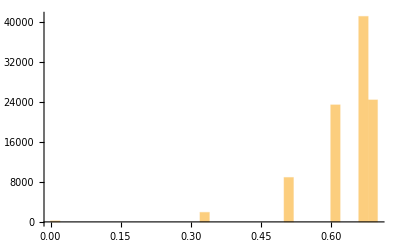

```mathematica
Histogram[Table[Entropy[Table[RandomInteger[],{i,1,10}]],{j,1,100000}]]
```

```mathematica
?*
```

```mathematica
Names["Sparse*`*Sparse*"]
```

{SparseArray`GraphToSparseMatrix,SparseArray`SparseArrayDimensions,SparseArray`SparseArrayFlatten,SparseArray`SparseArrayJoin,SparseArray`SparseArrayOp,SparseArray`SparseArrayRemoveDiagonal,SparseArray`SparseArrayScalingFactors,SparseArray`SparseArraySort,SparseArray`SparseArraySortedQ,SparseArray`SparseArrayTensorRank,SparseArray`SparseArrayTranspose,SparseArray`SparseBlockMatrix,SparseArray`SparseIdentityArray,SparseArray`SparseLUDecomposition,SparseArray`SparseMatrixApplyILU,SparseArray`SparseMatrixILU,SparseArray`SparseRuleForm,SparseArray`VectorToDiagonalSparseArray}

```mathematica
SparseArray`SparseArrayFlatten[
```

SparseArray`SparseArrayBlockMatrix[fdsfsd]

```mathematica
?"Sparse`*"
```

Information::nomatch: No symbol matching "Sparse`*" found.

```mathematica
iii88
```

```mathematica
Entropy[{1,1,0}]
Entropy[{0,1,1}]
Entropy[{1,0,1}]
```

2/3 Log[3/2]+Log[3]/3

2/3 Log[3/2]+Log[3]/3

2/3 Log[3/2]+Log[3]/3

```mathematica
2^10
```

```mathematica
Do[
```

0.673012

```mathematica
Entropy[{1,1,0}]//N
```

0.636514

```mathematica
QQ[[1]]
```

{{1,1,0,1,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},-40}

```mathematica
4*(5^6*8)
```

500000

```mathematica
zzz
```

SparseArray[<288768>, {2432, 2432}]

```mathematica
Γ[[1;;4,1;;7;;2]]
```

```mathematica
gg=SparseArray@(ConjugateTranspose[Γ].SparseArray@LinearSolve[Γ.ConjugateTranspose[Γ],Γ]//NullSpace//Chop);
```

```mathematica
Union@Map[Last,Map[First,Most@(Γ//ArrayRules)]]//Length
```

128

```mathematica
zzz=SparseArray@ArrayFlatten[{{0massQ,S,ConjugateTranspose[Ξ],0},{ConjugateTranspose[S],0,0,ConjugateTranspose[Γ]},{Ξ,0,0,0},{0,Γ,0,0}}];
```

```mathematica
zzz
```

SparseArray[<190464>, {2432, 2432}]

```mathematica
Eigenvalues[zzz,-1]
```

{0.0019009}

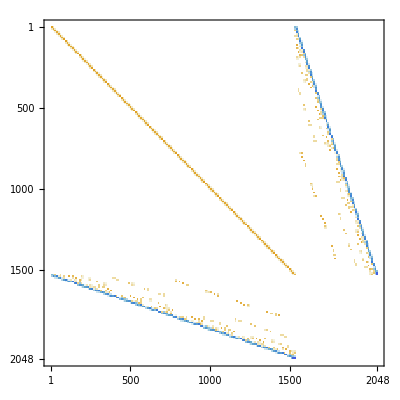

```mathematica
zzz//MatrixPlot
```

```mathematica
massU
```

SparseArray[<4096>, {512, 512}]

```mathematica
;
```

```mathematica
Γ.AA
```

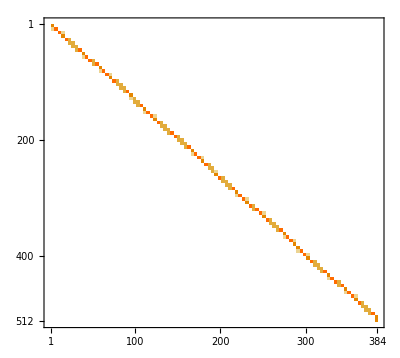

```mathematica
AA//MatrixPlot
```

```mathematica
A
```

```mathematica
QQ=B.yy+ConjugateTranspose[Ξ].𝓂𝓂;
UU=A.xx+ConjugateTranspose[Γ].ℓℓ;
```

```mathematica
zzz=
SparseArray@ArrayFlatten[
{{massQ,S,ConjugateTranspose[Ξ],0},{-ConjugateTranspose[R],0,0,ConjugateTranspose[Γ]},{Ξ,0,0,0},{0,Γ,0,0}
}
];
```

```mathematica
LinearSolve[zzz,Join[f,g,h,j],Method->"Automatic"]-Join[Q,U,μ,λ]//Norm
```

1.68023×10^-13

```mathematica
B//Dimensions
```

{18,12}

```mathematica
rhs=RandomReal[{-1,1},12]
```

{0.0113252,-0.682651,0.437283,0.277656,-0.157865,0.00112581,0.156139,-0.546335,0.295217,-0.221265,-0.507771,-0.274522}

```mathematica
bsmb[x_] := ConjugateTranspose[B].massQ.B.x
```

```mathematica
bsmb[x_] := ConjugateTranspose[B].massQ.B.x
bsmbInverse[x_] := LinearSolve[bsmb,x,Method->"Krylov"];
κ[x_] := ConjugateTranspose[A].ConjugateTranspose[S].B.bsmbInverse[ConjugateTranspose[B].S.A.x];
κInverse[x_] := LinearSolve[κ,x,Method->"Krylov"];
```

```mathematica
x=RandomReal[{-1,1},3];
κInverse[κ[x]]-x//Chop
```

{0,0,0}

```mathematica
Dimensions[A]
```

```mathematica
rhs=RandomReal[{-1,1},3]
```

```mathematica
κ[rhs]
```

{-0.566356,-0.73406,-2.7814}

```mathematica
LinearSolve[bsmb,rhs,Method->"Krylov"]
```

{0.603291,-0.581253,1.18279,0.87339,-0.208705,0.434123,0.147726,-0.0905378,0.187359,0.0754519,-0.132836,0.0724365}

```mathematica
Inverse[ConjugateTranspose[A].ConjugateTranspose[S].B.Inverse[ConjugateTranspose[B].massQ.B].ConjugateTranspose[B].S.A]
```

{{1.32694,0.804817,-0.388437},{0.804817,1.40625,-0.37853},{-0.388437,-0.37853,0.501186}}

```mathematica
Inverse[ConjugateTranspose[A].ConjugateTranspose[S].B.Inverse[ConjugateTranspose[B].massQ.B].ConjugateTranspose[B].S.A].(ConjugateTranspose[A].ConjugateTranspose[S].B.Inverse[ConjugateTranspose[B].massQ.B].FF+GG)
```

{0.572469,-0.0479341,0.663333}

```mathematica
ConjugateTranspose[B].S.A-ConjugateTranspose[B].R.A
```

{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}

```mathematica
ConjugateTranspose[B].massQ.B.y+  ConjugateTranspose[B].S.A.x- ( ConjugateTranspose[B].f-ConjugateTranspose[B].massQ.ConjugateTranspose[Ξ].LinearSolve[Ξ.ConjugateTranspose[Ξ],h]- ConjugateTranspose[B].S.ConjugateTranspose[Γ].LinearSolve[Γ.ConjugateTranspose[Γ],j])//Chop
Ξ.massQ.B.y+Ξ.S.A.x+Ξ.ConjugateTranspose[Ξ].μ-(Ξ.f-Ξ.S.ConjugateTranspose[Γ].LinearSolve[Γ.ConjugateTranspose[Γ],j]-Ξ.massQ.ConjugateTranspose[Ξ].LinearSolve[Ξ.ConjugateTranspose[Ξ],h])//Chop
-ConjugateTranspose[A].ConjugateTranspose[R].B.y-(ConjugateTranspose[A].g+ConjugateTranspose[A].ConjugateTranspose[R].ConjugateTranspose[Ξ].LinearSolve[Ξ.ConjugateTranspose[Ξ],h])//Chop

-Γ.ConjugateTranspose[R].B.y-Γ.ConjugateTranspose[R].ConjugateTranspose[Ξ].LinearSolve[Ξ.ConjugateTranspose[Ξ],h]+Γ.ConjugateTranspose[Γ].λ-Γ.g//Chop
```

{0,0,0,0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0}

{0,0,0}

{0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0}

{0,0,0}

{0,0,0,0,0,0}

```mathematica
LinearSolve[Ξ.ConjugateTranspose[Ξ],h]-𝓂
```

{-1.94289×10^-16,9.71445×10^-17,-2.22045×10^-16,-1.11022×10^-16,-1.11022×10^-16,5.55112×10^-16}

```mathematica
Ξ.B.y
```

{9.7752×10^-17,1.7939×10^-16,-3.68758×10^-17,-2.31859×10^-16,-8.43656×10^-17,7.39599×10^-18}

```mathematica
-ℓ//Chop
```

{0,0,0,0,0,0}

```mathematica
;
```

0

{1.325,7.84087,1.31741,-1.44043,-9.47005,-1.71554}

```mathematica
AAA-BBB//Expand//Chop
```

{0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ConjugateTranspose[B].massQ.ConjugateTranspose[Ξ].ℓ//Chop
```

{0,0,0,0,0,0,-0.0172199,-0.657974,-0.295988,0,0,0}

```mathematica
λλ=LinearSolve[Γ.Inverse[ConjugateTranspose[B].inverseMassQ.A].ConjugateTranspose[Γ],(Γ.Inverse[ConjugateTranspose[B].inverseMassQ.A].(ConjugateTranspose[B].inverseMassQ.f+g)-h)];
UU=LinearSolve[ConjugateTranspose[B].inverseMassQ.A,ConjugateTranspose[B].inverseMassQ.f+g-ConjugateTranspose[Γ].λ]
QQ=inverseMassQ.(f-A.UU)
```

```mathematica
QQ-Q//Chop
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
U
```

{-0.958204,-0.185892,-0.813071,-0.0921767,-0.523378,-0.101457,-0.832501,-0.444763,0.290826}

```mathematica
λ
LinearSolve[Γ.Inverse[ConjugateTranspose[B].inverseMassQ.A].ConjugateTranspose[Γ],Γ.LinearSolve[ConjugateTranspose[B].inverseMassQ.A,ConjugateTranspose[B].inverseMassQ.f+g]-h]
```

{0.762161,0.509757,-0.723584,-0.104056,0.775164,0.755243}

{0.762161,0.509757,-0.723584,-0.104056,0.775164,0.755243}

```mathematica
λ
```

{0.762161,0.509757,-0.723584,-0.104056,0.775164,0.755243}